# Universal Estimator

## Parameter range adjustment

For convenience, we want to work with parameters  ∈ (0,1) and map them to the parameters in the original range.
For that, we can use the Logistic function and its Logit inverse.

#### The Logistic function

The standard Logistic function, σ(x), defined in (-∞, ∞) and yields values in (0,1):

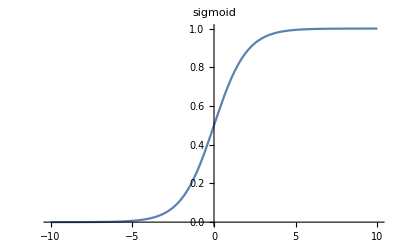

```mathematica
Sigmoid[x_]:=1/(1+ⅇ^-x)
Plot[Sigmoid[x], {x, -10, +10}, PlotLabel->HoldForm[sigmoid]]
```

#### The Logit function

The Logit  is the inverse of the Logistic function σ(x), defined in (0,1) and yields values in (-∞, ∞).
Let’s find the inverse:
σ(x) = y =  1/(1+e^-x) ⇒  1+e^-x = 1/y  ⇒  e^-x = 1/y-1=(1-y)/y  ⇒  log(e^-x)=log((1-y)/y)  ⇒  -x = log((1-y)/y)  ⇒  x = log(y/(1-y)) = σ^-1(x)

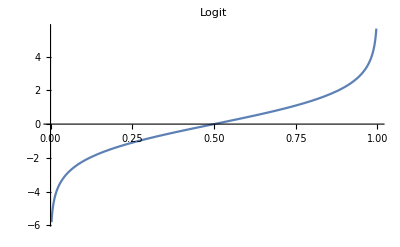

```mathematica
Logit[x_]:= Log[x/(1-x)]
Plot[Logit[x], {x, 0, 1}, PlotLabel->HoldForm[Logit]]
```

### Range Adjuster

We define an Adjuster function which returns another function that maps a parameter in the range  (0,1) to the range  (low, high) of the original distribution.
We can use the Logistic function and its Logit inverse as follows:
Let
	h(t) = Logit(t) , t ∈ (0,1)
Than
	h^-1(d) = Sigmoid(d) , d ∈ (-∞, ∞)

```mathematica
Adjuster[low_, high_]:=With[{LOW=Sigmoid[low],HIGH=Sigmoid[high]}, Function[{t},Logit[LOW+t(HIGH-LOW)]]]
```

### Test Adjuster

For example, we can create an Adjuster for the range [2,5] and call it with values ∈ [0,1]

```mathematica
adj=Adjuster[2, 5];
Print[adj[0.01]];
```

2.01076

```mathematica
Print[adj[0.99]];
```

4.84348

Plot of the adjuster output in the range [0,1]

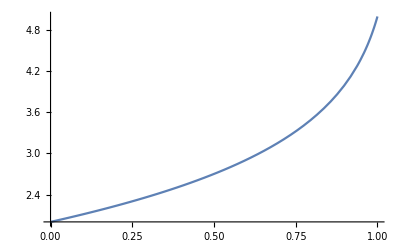

```mathematica
Print[Plot[adj[x], {x,0,1}]]
```

## Generate data

Arguments:

nSamples: number of samples

M: number of observations in each sample

f: the function to generate samples

ranges: an array [d X 2] of parameter ranges (e.g. for 2 parameters: [[0, 10], [0, ∞]])

bins: number of bins in histograms (default: max[samples]+1)

Returns:

samples, params, histograms

```mathematica
GenerateData[nSamples_, M_, f_, ranges_, bins_:-1]:= 
Module[{nParams, adjusters, params, samples, nbins, histograms},

(*number of parameters*)
nParams=Dimensions[ranges][[1]];

(*generate an adapter for each parameter range*)
adjusters=Table[Adjuster[ranges[[i,1]],ranges[[i,2]]],{i,1,nParams}];

(*generate N parameters cube in the range (0,1)*)
params=Table[adjusters[[j]][RandomReal[{0,1}]],{i,1,nSamples},{j,1,nParams}];

(*generate N samples from the parameters*)
samples=Table[f[params[[i]],M],{i,1,nSamples}];

(*create a histogram for each sample*)
nbins=If [bins>0,bins,Max[samples]+1];
h[x_]:=HistogramList[x, {0,nbins,1}][[2]];
histograms=Map[h,samples];

(*output*)
{params,samples, histograms}
]
```

Test GenerateData

```mathematica
YuleSimon[{alpha_,beta_}, size_]:=RandomVariate[WaringYuleDistribution[alpha,beta],size];
YuleSimonRanges = {{2,3},{0,10}};

data = GenerateData[5,20,YuleSimon, YuleSimonRanges];

Print["params:"];
Print[data[[1]]// TableForm];
Print["samples:"];
Print[data[[2]]// TableForm];
Print["histograms:"];
Print[data[[3]]// TableForm];
```

params:

2.35968 | 2.16533
2.11367 | 0.750055
2.86162 | 0.713064
2.83545 | 2.85122
2.88798 | 1.18247

samples:

0 | 3 | 0 | 1 | 0 | 0 | 1 | 0 | 2 | 1 | 0 | 2 | 0 | 2 | 1 | 3 | 0 | 0 | 0 | 3
0 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 3 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 20 | 4 | 0 | 0 | 0 | 0 | 0 | 3 | 1 | 3 | 2 | 0 | 0 | 2 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 6 | 0 | 0 | 1 | 0 | 0 | 4 | 2 | 1 | 0 | 1 | 0

histograms:

10 | 4 | 3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16 | 2 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16 | 3 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12 | 2 | 2 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
13 | 3 | 2 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

## Define DNN

```mathematica
CreateNet[M_, nOutputs_]:=( 
NetInitialize@NetChain[{
LinearLayer[M], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp],
LinearLayer[M], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 
LinearLayer[nOutputs]},
"Input"->M, 
"Output" -> nOutputs]
)
```

```mathematica
M = 256;
nParams=Dimensions[YuleSimonRanges][[1]];
net = CreateNet[M, nParams];
Print[NetGraph[net]];
```

NetGraph[<>]

```mathematica
nSamples = 1000;
trainingset=GenerateData[nSamples,M,YuleSimon, YuleSimonRanges];
trained=NetTrain[net,trainingset,Method->"ADAM"];
```

NetTrain::invtdata: Training data should be an association of lists, or a rule from input to output examples.

## Experiments

```mathematica
results = Import["/home/yossi/Documents/Wolfram Mathematica/cached_mesh_points.csv"];
Print[results//TableForm];

(*dict["sample"] = YuleSimon
dict["ranges"] = {{2,3},{0,10}}
dict["M"] = 256
f = dict["sample"]
ranges = dict["ranges"]
f[ranges[[1,1]], dict["M"]]
*)
```

mesh_point | param1_test | param2_test | param1_pred | param2_pred | mse
0.1|0.1 | 2.07022 | 0.200671 | 2.1178 | 0.514067 | 0.0645134
0.1|0.2 | 2.07022 | 0.405465 | 2.30208 | 0.547817 | 0.0461519
0.1|0.3 | 2.07022 | 0.619039 | 2.07718 | 0.389102 | 0.0410234
0.1|0.4 | 2.07022 | 0.847298 | 2.13102 | 0.456833 | 0.0839418
0.1|0.5 | 2.07022 | 1.09861 | 2.1968 | 1.40629 | 0.0617095
0.1|0.6 | 2.07022 | 1.38629 | 2.32311 | 1.47971 | 0.0412682
0.1|0.7 | 2.07022 | 1.7346 | 2.17566 | 1.59212 | 0.0305189
0.1|0.8 | 2.07022 | 2.19722 | 2.19324 | 2.40877 | 0.0369091
0.1|0.9 | 2.07022 | 2.94444 | 2.20141 | 2.50929 | 0.107362
0.2|0.1 | 2.14449 | 0.200671 | 2.39358 | 0.466635 | 0.0700949
0.2|0.2 | 2.14449 | 0.405465 | 2.27024 | 0.492381 | 0.0132611
0.2|0.3 | 2.14449 | 0.619039 | 2.31856 | 0.495535 | 0.0259109
0.2|0.4 | 2.14449 | 0.847298 | 2.03473 | 0.460183 | 0.0892586
0.2|0.5 | 2.14449 | 1.09861 | 2.39132 | 1.44789 | 0.0937052
0.2|0.6 | 2.14449 | 1.38629 | 2.29876 | 1.42068 | 0.0192241
0.2|0.7 | 2.14449 | 1.7346 | 2.19587 | 1.43784 | 0.0584538
0.2|0.8 | 2.14449 | 2.19722 | 2.22153 | 2.3646 | 0.0259576
0.2|0.9 | 2.14449 | 2.94444 | 2.11586 | 2.37137 | 0.167625
0.3|0.1 | 2.22339 | 0.200671 | 2.24013 | 0.458839 | 0.0367979
0.3|0.2 | 2.22339 | 0.405465 | 2.63072 | 0.481393 | 0.0903806
0.3|0.3 | 2.22339 | 0.619039 | 2.2368 | 0.464432 | 0.0179884
0.3|0.4 | 2.22339 | 0.847298 | 2.40846 | 0.532003 | 0.0757238
0.3|0.5 | 2.22339 | 1.09861 | 2.51521 | 1.47173 | 0.115791
0.3|0.6 | 2.22339 | 1.38629 | 2.45889 | 1.4374 | 0.0362468
0.3|0.7 | 2.22339 | 1.7346 | 2.52641 | 1.4259 | 0.0963959
0.3|0.8 | 2.22339 | 2.19722 | 2.30112 | 2.40347 | 0.0298634
0.3|0.9 | 2.22339 | 2.94444 | 2.22115 | 2.50868 | 0.100907
0.4|0.1 | 2.30764 | 0.200671 | 2.23157 | 0.506455 | 0.0515556
0.4|0.2 | 2.30764 | 0.405465 | 2.47623 | 0.567762 | 0.0399008
0.4|0.3 | 2.30764 | 0.619039 | 2.13613 | 0.378672 | 0.0457681
0.4|0.4 | 2.30764 | 0.847298 | 2.25115 | 0.53623 | 0.0721657
0.4|0.5 | 2.30764 | 1.09861 | 2.16314 | 1.47991 | 0.0841811
0.4|0.6 | 2.30764 | 1.38629 | 2.54822 | 1.45062 | 0.0396965
0.4|0.7 | 2.30764 | 1.7346 | 2.58191 | 1.42821 | 0.092007
0.4|0.8 | 2.30764 | 2.19722 | 2.33234 | 2.45616 | 0.0469676
0.4|0.9 | 2.30764 | 2.94444 | 2.21913 | 2.50861 | 0.116866
0.5|0.1 | 2.39814 | 0.200671 | 2.47953 | 0.458509 | 0.0508142
0.5|0.2 | 2.39814 | 0.405465 | 2.32732 | 0.433603 | 0.0091996
0.5|0.3 | 2.39814 | 0.619039 | 2.47755 | 0.539271 | 0.00827623
0.5|0.4 | 2.39814 | 0.847298 | 2.38353 | 0.491008 | 0.0655916
0.5|0.5 | 2.39814 | 1.09861 | 2.31976 | 1.41581 | 0.0586346
0.5|0.6 | 2.39814 | 1.38629 | 2.20684 | 1.43021 | 0.0274824
0.5|0.7 | 2.39814 | 1.7346 | 2.31566 | 1.42144 | 0.0538297
0.5|0.8 | 2.39814 | 2.19722 | 2.44001 | 2.32782 | 0.0111358
0.5|0.9 | 2.39814 | 2.94444 | 2.31588 | 2.28147 | 0.232476
0.6|0.1 | 2.49603 | 0.200671 | 2.49349 | 0.504579 | 0.049759
0.6|0.2 | 2.49603 | 0.405465 | 2.16577 | 0.423811 | 0.0645338
0.6|0.3 | 2.49603 | 0.619039 | 2.30487 | 0.560477 | 0.0229145
0.6|0.4 | 2.49603 | 0.847298 | 2.55336 | 0.473118 | 0.0782807
0.6|0.5 | 2.49603 | 1.09861 | 2.52858 | 1.45327 | 0.0661113
0.6|0.6 | 2.49603 | 1.38629 | 2.66995 | 1.37949 | 0.0198562
0.6|0.7 | 2.49603 | 1.7346 | 2.59175 | 1.44591 | 0.0533006
0.6|0.8 | 2.49603 | 2.19722 | 2.45901 | 2.37317 | 0.0432876
0.6|0.9 | 2.49603 | 2.94444 | 2.40857 | 2.47361 | 0.144274
0.7|0.1 | 2.60279 | 0.200671 | 2.5621 | 0.571538 | 0.0710431
0.7|0.2 | 2.60279 | 0.405465 | 2.34314 | 0.456907 | 0.0367186
0.7|0.3 | 2.60279 | 0.619039 | 2.70416 | 0.497987 | 0.0178964
0.7|0.4 | 2.60279 | 0.847298 | 2.52585 | 0.60227 | 0.0469073
0.7|0.5 | 2.60279 | 1.09861 | 2.42321 | 1.41379 | 0.0753988
0.7|0.6 | 2.60279 | 1.38629 | 2.32124 | 1.40876 | 0.0451636
0.7|0.7 | 2.60279 | 1.7346 | 2.57095 | 1.44694 | 0.053954
0.7|0.8 | 2.60279 | 2.19722 | 2.25009 | 2.48444 | 0.104881
0.7|0.9 | 2.60279 | 2.94444 | 2.51829 | 2.46395 | 0.143246
0.8|0.1 | 2.72038 | 0.200671 | 2.36902 | 0.509137 | 0.110693
0.8|0.2 | 2.72038 | 0.405465 | 2.54703 | 0.504698 | 0.0232278
0.8|0.3 | 2.72038 | 0.619039 | 2.50187 | 0.606356 | 0.0306704
0.8|0.4 | 2.72038 | 0.847298 | 2.65737 | 0.557637 | 0.0461103
0.8|0.5 | 2.72038 | 1.09861 | 2.24029 | 1.46506 | 0.183423
0.8|0.6 | 2.72038 | 1.38629 | 2.66799 | 1.36233 | 0.00382952
0.8|0.7 | 2.72038 | 1.7346 | 2.44623 | 1.43078 | 0.0905788
0.8|0.8 | 2.72038 | 2.19722 | 2.31067 | 2.38288 | 0.153522
0.8|0.9 | 2.72038 | 2.94444 | 2.36592 | 2.37651 | 0.238389
0.9|0.1 | 2.8515 | 0.200671 | 2.64314 | 0.570747 | 0.0994111
0.9|0.2 | 2.8515 | 0.405465 | 2.76887 | 0.474565 | 0.0182493
0.9|0.3 | 2.8515 | 0.619039 | 2.35297 | 0.509515 | 0.131843
0.9|0.4 | 2.8515 | 0.847298 | 2.54762 | 0.418737 | 0.149546
0.9|0.5 | 2.8515 | 1.09861 | 2.55801 | 1.44012 | 0.114366
0.9|0.6 | 2.8515 | 1.38629 | 2.40658 | 1.33192 | 0.151461
0.9|0.7 | 2.8515 | 1.7346 | 2.70428 | 1.49251 | 0.0590361
0.9|0.8 | 2.8515 | 2.19722 | 2.5673 | 2.4378 | 0.0884625
0.9|0.9 | 2.8515 | 2.94444 | 2.53413 | 2.41155 | 0.205646